# Evolution settings author: Alexei Prokudin email: prokudin@jlab.org

## Constants

```mathematica
ProduceGrids = False; (* Make it True if you want the program to produce grids for WW relations *)

Mproton = 0.93827;
Mp = Mproton;
Mpion = 0.13957;
scompass = 2*Mproton*190.;
Q2compass= 28.;
Q2min=4.3^2;Q2max=8.5^2;


(* Implement the broadening 
pbroad = 0.7 10^-3;
pionbroad =2.1 10^-3;
*)
(* Implement the broadening new way*)
(* kwa and kwb are the Guassian widths and the arguments represent U=Unpolarized, T=Transversity, S=Sivers, BM=Boer-Mulders, P=Pretzelosity, WG=Worm-Gear (Subscript[h, 1L]^⊥) *) 
kwb["U"]=0.25;kwa["U"]=0.25; (* Widths from arxiv:1003.2190 *)
kwb["T"]=kwb["U"];kwb["WG"]=kwb["T"];kwa["BM"]=kwb["BM"];

(* Broadening for three different cases; [U,U],[P,U],[P,P] *)
(* A and B can be U,T,S,BM,P or WG labeling the TMDs*)
(* P[A] categorizes the TMDs to unpolarizes and polarized quark distributions *)
qw[A_,B_]:=δ[P[A],P[B]]
P[A_]:=If[A=="U","U","P"]
δ["U","U"]=δUU;δ["U","P"]=δPU;δ["P","U"]=δPU;δ["P","P"]=δPP;
δUU=1.5;δPP=1.2;δPU=1.3;

qw["U","U"];
qw["U","P"];
qw["BM","S"];

Λ = 0.2;
CF = 4/3;
CA=3;
TR = 0.5;
Nf = 3;
beta0 = (33 - 2 Nf)/(12 π);
Q0 = 1.3;  (* Starting scale for evolution. *)
(*Q0 = 0.45; (* Starting scale for evolution fro models. *) *)
MZ = 91.19;

bmax = 1.;


g0CSS = (as[C1/bmax] CF)/π ; (* it is the lower limit, actually, can be bigger, see discussion after Eq. (83) from PRD 91*)

g0YUAN = 0.84;

g0 = g0YUAN;



bstar[bt_] := bt/ Sqrt[1 + bt^2 / bmax^2]; (* b* *)


C1 = 2 Exp[-N[EulerGamma]];   
mub[bt_] := C1 / bstar[bt]; (* mub *)
```

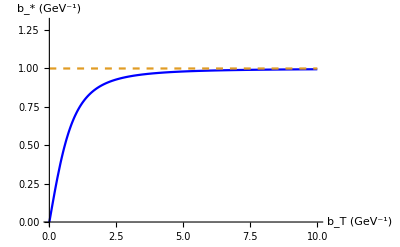

```mathematica
Plot[{bstar[bt],bmax},{bt,0,10},AxesLabel->{"b_T (GeV^-1)","b_* (GeV^-1)"},PlotRange->{0,1.3},PlotStyle->{Blue,Dashed}]
```

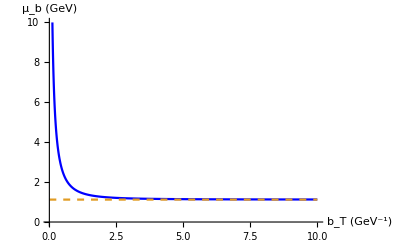

```mathematica
Plot[{mub[bt],C1/bmax},{bt,0,10},AxesLabel->{"b_T (GeV^-1)","μ_b (GeV)"},PlotRange->{0,10},PlotStyle->{Blue,Dashed}]
```

## QCD strong coupling, alpha s

#### Let us start by constructing a 2 loop solution compatible with CTEQ parametrization

```mathematica
Lambda[Q_]:=Piecewise[{{0.372205,Q≤1.3},{0.325603,1.3≤Q<4.5},{0.2259965,4.5≤Q}}];
NF[Q_]:=Piecewise[{{3,Q≤1.3},{4,1.3≤Q<4.5},{5,4.5≤Q}}];
β[Q_]:=11-2/3 NF[Q];
β1[Q_]:=51-19/3 NF[Q];

AlphaS[Q_]:=
(4π)/(β[Q]Log[Q^2/Lambda[Q]^2])(1-(2β1[Q])/β[Q]^2 Log[Log[Q^2/Lambda[Q]^2]]/Log[Q^2/Lambda[Q]^2])
```

```mathematica
AlphaS[MZ]
```

0.117981

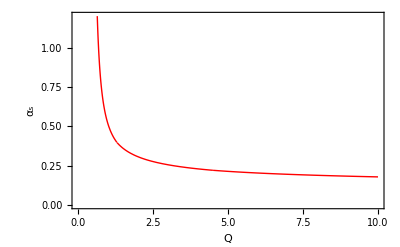

```mathematica
Plot[AlphaS[Q],{Q,0.5,10},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,10},{0,1.2}},PlotStyle->{{Thick,Red},{Thick,Blue,Dashed},{Thick,Red,Dashed},{Thick,Blue,Dashed}}, FrameLabel->{"Q","α_s"},BaseStyle->{FontSize->16,FontFamily->"Times New Roman"},LabelStyle->Directive[FontFamily->"Times New Roman"]]
```

#### Let us also use a simple solution that we will “tune” to the 2 loop one in the region of interest Q in 1.3 (our initial scale) to 10

```mathematica
as[Q_]:= 1/(beta0 Log[Q^2/Λ^2])
```

Clearly at very high Q solutions will diverge from each other, i.e. at MZ

```mathematica
as[MZ]
AlphaS[MZ]
```

0.114029

0.117981

```mathematica
as[0.45]
```

0.860902

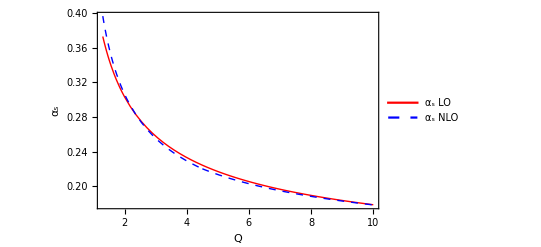

```mathematica
Plot[{as[Q],AlphaS[Q]},{Q,1.3,10},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotStyle->{{Thick,Red},{Thick,Blue,Dashed},{Thick,Red,Dashed},{Thick,Blue,Dashed}}, FrameLabel->{"Q","α_s"},BaseStyle->{FontSize->16,FontFamily->"Times New Roman"},LabelStyle->Directive[FontFamily->"Times New Roman"],PlotLegends->Placed[{"α_s LO","α_s NLO"},{0.7,0.7}]]
```

## Perturbative evolution

One loop result using one loop alpha_s

```mathematica
A1[mu_] := CF;
B1[mu_]:=-3/2 CF;
(*A2[mu_]:=CF/2 (CA (67/18-π^2/6)-10/9 TR NF[mu]);*) (* Do we have to change number of flavors???*)
A2[mu_]:=CF/2 (CA (67/18-π^2/6)-10/9 TR Nf);
A[mu_] := AlphaS[mu]/π A1[mu] +(AlphaS[mu]/π)^2 A2[mu];
B[mu_] := AlphaS[mu]/π B1[mu];
Spert[Q_,Q0_]:= NIntegrate[2/mu (A[mu] Log[Q^2/Q0^2]+B[mu]),{mu,Q0,Q}];
```

```mathematica
Spert[Sqrt[Q2compass],Q0]
```

0.634016

```mathematica
Spert1[Q_,Q0_]:=-(2 CF)/(π beta0)(Log[Q/Q0]-Log[Q/Λ]Log[Log[Q/Λ]/Log[Q0/Λ]]+3/4 Log[Log[Q/Λ]/Log[Q0/Λ]])
```

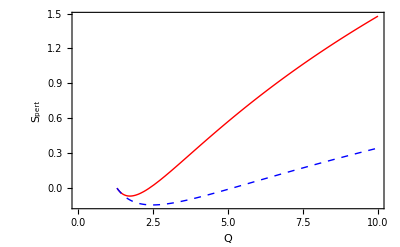

```mathematica
Plot[{Spert[Q,Q0],Spert1[Q,Q0]},{Q,Q0,10},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,10},Automatic},PlotStyle->{{Thick,Red},{Thick,Blue,Dashed},{Thick,Red,Dashed},{Thick,Blue,Dashed}}, FrameLabel->{"Q","S_pert"},BaseStyle->{FontSize->16,FontFamily->"Times New Roman"},LabelStyle->Directive[FontFamily->"Times New Roman"]]
```

Notice Sperp becomes negative.

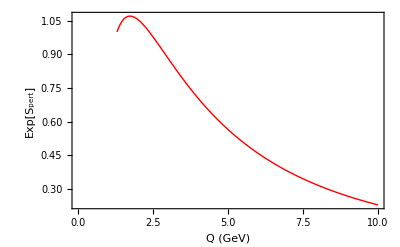

```mathematica
Plot[Exp[-Spert[Q,Q0]],{Q,Q0,10},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,10},Automatic},PlotStyle->{{Thick,Red},{Thick,Blue,Dashed},{Thick,Red,Dashed},{Thick,Blue,Dashed}}, FrameLabel->{"Q (GeV)","Exp[S_pert]"},BaseStyle->{FontSize->16,FontFamily->"Times New Roman"},LabelStyle->Directive[FontFamily->"Times New Roman"]]
```

```mathematica
Export["../tex/figs/spert.pdf",%,Background->None]
```

Export::nodir: Directory /Users/tex/figs/ does not exist.

Export::noopen: Cannot open ../tex/figs/spert.pdf.

$Failed

It results in an enhancement instead of suppression for some region in Q.

## Collins-Soper evolution kernel K̃ , it gives the Q-dependent change in the distribution, a very characteristic effect of the gluon emissions

One loop solution:

```mathematica
KtildePert[b_,Q_]:= -as[Q]/π(Log[(b^2 Q^2)/4]+ 2 N[EulerGamma])
```

```mathematica
Plot3D[KtildePert[b,Q],{b,0,1},{Q,Q0,10}]
```

-Graphics3D-

It looks like this at the initial scale Q0:

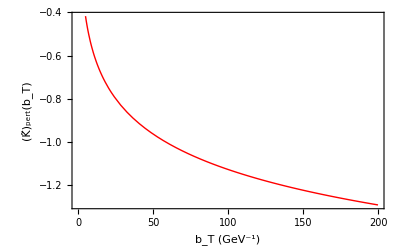

```mathematica
Plot[KtildePert[b,Q0],{b,0,200},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotStyle->{{Thick,Red},{Thick,Blue,Dashed},{Thick,Red,Dashed},{Thick,Blue,Dashed}}, FrameLabel->{"b_T (GeV^-1)","(K̃)_pert(b_T)"},BaseStyle->{FontSize->16,FontFamily->"Times New Roman"},LabelStyle->Directive[FontFamily->"Times New Roman"]]
```

At large values of b, K̃, tends to a negative constant

K̃ from Collins, Rogers PRD 91,(2015)
 
 gK from Eq.(79)

```mathematica
gK[b_] := g0 ( 1-Exp[-(as[mub[b]] CF b^2)/(π g0 bmax^2) ]); (*model for non perturbative dynamics in CS kernel from PRD 91*)
gKYuan[b_] := g0YUAN Log[b/bstar[b]];  (* this one is from my paper with Kang and Yan *)
```

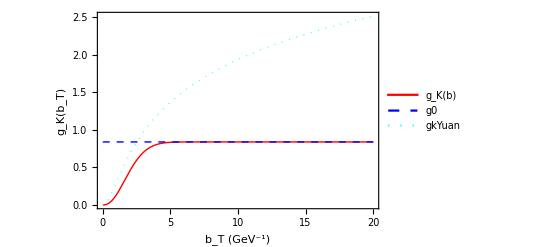

```mathematica
Plot[{gK[b],g0,gKYuan[b]},{b,0.01,20},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotStyle->{{Thick,Red},{Thick,Blue,Dashed},{Thick,Cyan,Dotted}}, FrameLabel->{"b_T (GeV^-1)","g_K(b_T)"},BaseStyle->{FontSize->16,FontFamily->"Times New Roman"},LabelStyle->Directive[FontFamily->"Times New Roman"],PlotLegends->Placed[{"g_K(b)", "g0","gkYuan" },{0.7,0.7}]]
```

K̃ from Collins, Rogers PRD 91,(2015)
 
 K̃ from Eq. (64) Collins, Rogers PRD 91,(2015)

```mathematica
KtildeLL[b_,Q0_]:= KtildePert[bstar[b],mub[b]]-CF/(π beta0)Log[Log[Q0/Λ]/Log[mub[b]/Λ]]- gK[b];
```

See https : // mathematica.stackexchange.com/questions/10533/nested - nintegrate for explanation of ?NumericQ

```mathematica
KtildeLL1[b_?NumericQ,Q0_?NumericQ]:= KtildePert[bstar[b],mub[b]]- NIntegrate[2/mu AlphaS[mu]/π A1[mu],{mu,mub[b],Q0}]- gK[b];
```

```mathematica
RGrunningKtilde[b_?NumericQ,Q0_?NumericQ]:=NIntegrate[2/mu A[mu] ,{mu,mub[b],Q0}];
```

```mathematica
(*Ktilde[b_?NumericQ,Q0_?NumericQ]:=Ktilde[b,Q0]= KtildePert[bstar[b],mub[b]]- NIntegrate[2/mu A[mu] ,{mu,mub[b],Q0}]- gK[b];*)
Ktilde[b_?NumericQ,Q0_?NumericQ]:=Ktilde[b,Q0]= KtildePert[bstar[b],mub[b]]- RGrunningKtilde[b,Q0]- gK[b];
```

Actually KtildePert[bstar[b], mub[b]] = 0!

```mathematica
ClearAll[Ktilde];
(*Ktilde[b_?NumericQ,Q0_?NumericQ]:= - NIntegrate[2/mu A[mu] ,{mu,mub[b],Q0}]- gK[b];*)
(* Ktildemub2loops[mub_] := 8 CF AlphaS[mub]^2 ((7/2 Zeta[3.]-101/27) CA + 14/27 Nf); *)
Ktilde[b_?NumericQ,Q0_?NumericQ]:=-RGrunningKtilde[b,Q0]- gK[b];
```

```mathematica
KtildeYuan[b_,Q0_]:= KtildePert[bstar[b],mub[b]]-CF/(π beta0)Log[Log[Q0/Λ]/Log[mub[b]/Λ]]- gKYuan[b];
```

```mathematica
Ktildemub2loops[mub[1.]]
```

3.81287

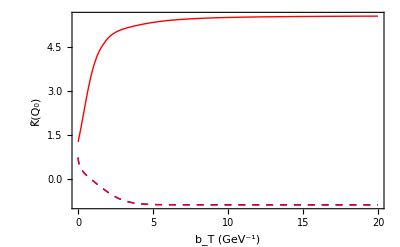

```mathematica
Plot[{Ktilde[b,Q0],KtildeLL[b,Q0],KtildeLL1[b,Q0]},{b,0.01,20},PlotRange->{{0,20},Automatic},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotStyle->{{Thick,Red},{Thick,Blue,Dashed},{Thick,Red,Dashed},{Thick,Blue,Dashed}}, FrameLabel->{"b_T (GeV^-1)","K̃(Q_0)"},BaseStyle->{FontSize->16,FontFamily->"Times New Roman"},LabelStyle->Directive[FontFamily->"Times New Roman"]]
```

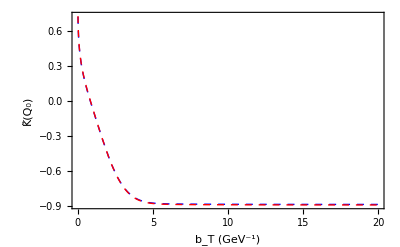

```mathematica
Plot[{Ktilde[b,Q0],KtildeLL[b,Q0],KtildeLL1[b,Q0]},{b,0.01,20},PlotRange->{{0,20},{1,-1.5}},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotStyle->{{Thick,Red},{Thick,Blue,Dashed},{Thick,Red,Dashed},{Thick,Blue,Dashed}}, FrameLabel->{"b_T (GeV^-1)","K̃(Q_0)"},BaseStyle->{FontSize->16,FontFamily->"Times New Roman"},LabelStyle->Directive[FontFamily->"Times New Roman"]]
```

```mathematica
Export["../tex/figs/Ktilde.pdf",%,Background->None]
```

Export::nodir: Directory /Users/tex/figs/ does not exist.

Export::noopen: Cannot open ../tex/figs/Ktilde.pdf.

$Failed

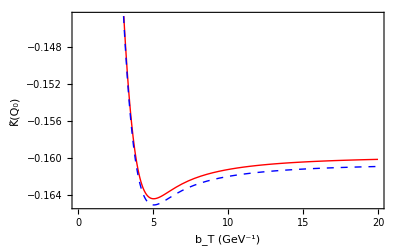

```mathematica
Plot[{KtildeLL[b,Q0]/Ktilde[b,Q0],KtildeLL1[b,Q0]/Ktilde[b,Q0]},{b,0.01,20},PlotRange->{{0,20},Automatic},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotStyle->{{Thick,Red},{Thick,Blue,Dashed},{Thick,Red,Dashed},{Thick,Blue,Dashed}}, FrameLabel->{"b_T (GeV^-1)","K̃(Q_0)"},BaseStyle->{FontSize->16,FontFamily->"Times New Roman"},LabelStyle->Directive[FontFamily->"Times New Roman"]]
```

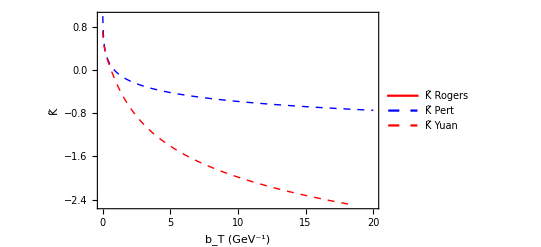

```mathematica
Plot[{Ktilde[b,Q0],KtildePert[b,Q0],KtildeYuan[b,Q0]},{b,0.01,20},PlotRange->{{0,20},{1,-2.5}},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotStyle->{{Thick,Red},{Thick,Blue,Dashed},{Thick,Red,Dashed},{Thick,Blue,Dashed}}, FrameLabel->{"b_T (GeV^-1)","K̃"},BaseStyle->{FontSize->16,FontFamily->"Times New Roman"},LabelStyle->Directive[FontFamily->"Times New Roman"],PlotLegends->Placed[{"K̃ Rogers", "K̃ Pert","K̃ Yuan" },{0.7,0.7}]]
```

```mathematica
EvolutionFactor[b_,Q2_]:= Exp[Ktilde[b,Q0] Log[Q2/Q0^2]]Exp[-Spert[Sqrt[Q2],Q0]];
```

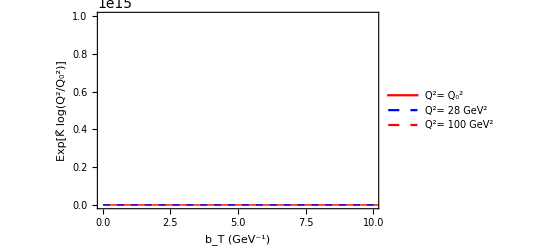

```mathematica
Plot[{Exp[Ktilde[b,Q0] Log[Q0^2/Q0^2]], Exp[Ktilde[b,Q0] Log[Q2compass/Q0^2]],Exp[Ktilde[b,Q0] Log[(100.*100.)/Q0^2]]},{b,0.01,20},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,10},Automatic},PlotStyle->{{Thick,Red},{Thick,Blue,Dashed},{Thick,Red,Dashed},{Thick,Blue,Dashed}}, FrameLabel->{"b_T (GeV^-1)","Exp[K̃ log(Q^2/Q_0^2)]"},BaseStyle->{FontSize->16,FontFamily->"Times New Roman"},LabelStyle->Directive[FontFamily->"Times New Roman"],PlotLegends->Placed[{"Q^2= Q_0^2","Q^2= 28 GeV^2","Q^2= 100 GeV^2"},{0.7,0.7}]]
```

```mathematica
Export["../tex/figs/expKtilde.pdf",%,Background->None]
```

Export::nodir: Directory /Users/tex/figs/ does not exist.

Export::noopen: Cannot open ../tex/figs/expKtilde.pdf.

$Failed

```mathematica
avk = 0.25;
Plot[{Exp[-(b^2 avk)/4] EvolutionFactor[b,Q0^2], Exp[-(b^2 avk)/4] EvolutionFactor[b,Q2compass],Exp[-(b^2 avk)/4]EvolutionFactor[b,100.*100.]},{b,0.01,20},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,10},{0,2}},PlotStyle->{{Thick,Red},{Thick,Blue,Dashed},{Thick,Red,Dashed},{Thick,Blue,Dashed}}, FrameLabel->{"b_T (GeV^-1)","Exp[S] Exp[-b^2/4]"},BaseStyle->{FontSize->16,FontFamily->"Times New Roman"},LabelStyle->Directive[FontFamily->"Times New Roman"],PlotLegends->Placed[{"Q^2= Q_0^2","Q^2= 28 GeV^2","Q^2= 100 GeV^2"},{0.7,0.7}]]
```

$Aborted

```mathematica
Export["../tex/figs/expS.pdf",%,Background->None]
```

Export::nodir: Directory /Users/tex/figs/ does not exist.

Export::noopen: Cannot open ../tex/figs/expS.pdf.

$Failed

```mathematica
pdf[kT_,Q2_ ]:= NIntegrate[b/(2 π) BesselJ[0,kT b] Exp[-(b^2 avk)/4]Sqrt[EvolutionFactor[b,Q2]],{b,0,100},MaxPoints-> 100];
```

```mathematica
pdf[0.1,Q2compass]
```

NIntegrate::maxp: The integral failed to converge after 101 integrand evaluations. NIntegrate obtained 0.123777 and 0.103838 for the integral and error estimates.

0.123777

## Solution optimized for perturbative calculations (aka original CSS)

```mathematica
gKCSS[b_] := (as[mub[b]] CF)/π Log[1+b^2/bmax^2]; (*model for non perturbative dynamics in CS kernel from PRD 91*)
```

We observe typical narrowing of the distribution in b as Q grows

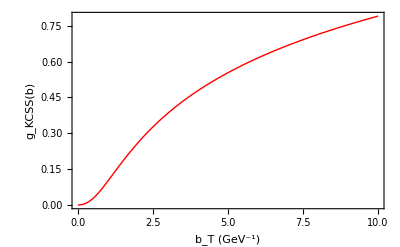

```mathematica
Plot[{gKCSS[b]},{b,0.01,10},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotStyle->{{Thick,Red},{Thick,Blue,Dashed},{Thick,Red,Dashed},{Thick,Blue,Dashed}}, FrameLabel->{"b_T (GeV^-1)","g_KCSS(b)"},BaseStyle->{FontSize->16,FontFamily->"Times New Roman"},LabelStyle->Directive[FontFamily->"Times New Roman"]]
```

```mathematica
EvolutionFactorCSS[b_,Q2_]:=Exp[-gKYuan[b] Log[Q2/Q0^2]]Exp[-Spert[Sqrt[Q2],mub[b]]]; 
(*EvolutionFactorCSS[b_,Q2_]:=Exp[-gKCSS[b] Log[Q2/Q0^2]]Exp[-Spert[Sqrt[Q2],mub[b]]];*)
```

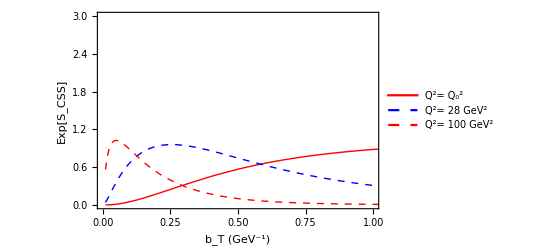

```mathematica
Plot[{EvolutionFactorCSS[b,Q0*Q0],EvolutionFactorCSS[b,Q2compass],EvolutionFactorCSS[b,1000]},{b,0.01,20},PlotRange->{{0,1},{0,3}},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotStyle->{{Thick,Red},{Thick,Blue,Dashed},{Thick,Red,Dashed},{Thick,Blue,Dashed}}, FrameLabel->{"b_T (GeV^-1)","Exp[S_CSS]"},BaseStyle->{FontSize->16,FontFamily->"Times New Roman"},LabelStyle->Directive[FontFamily->"Times New Roman"],PlotLegends->Placed[{"Q^2= Q_0^2","Q^2= 28 GeV^2","Q^2= 100 GeV^2" },{0.7,0.7}]]
```